## Scan k, 000 state, κ=0.61, mf=0.48

## b=(0,1) GeV^-1

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg=Join[{{0.05,111.30321176278534},{0.15000000000000002,11.43261216229469},{0.25,3.760286171713003},{0.35000000000000003,1.7688791757891529},{0.45,1.00277521993155},{0.55,0.6374688302691097},{0.6500000000000001,0.43730056194001216},{0.7500000000000001,0.31594072602820694},{0.8500000000000001,0.23652490238951984},{0.9500000000000001,0.18184596440765863},{1.05,0.14248554895070756},{1.1500000000000001,0.11348227231852108},{1.2500000000000002,0.091593377652407},{1.35,0.07470445404126752},{1.4500000000000002,0.061570556050017246},{1.55,0.05116484610632678},{1.6500000000000001,0.04285658863183254},{1.7500000000000002,0.0361717826648325},{1.85,0.030745031857356858},{1.9500000000000002,0.02628987952619396}},{{2.,0.024380037511776247},{2.2,0.0182457426947517},{2.4,0.013912233570619395},{2.6,0.010789499083747715},{2.8,0.008508372010541491},{3.,0.006796678574139209},{3.2,0.005503668798760963},{3.4000000000000004,0.004497918752417921},{3.6,0.0037127094291362983},{3.8,0.0030939001076985824},{4.,0.0026007701312458858},{4.2,0.0022023916545900733},{4.4,0.0018787359886929195},{4.6,0.0016138804600683875},{4.800000000000001,0.001390831835355987},{5.,0.0012082958401848042},{5.2,0.001054102768522289},{5.4,0.0009243321717898566},{5.6,0.0008138325791250697},{5.800000000000001,0.0007191526043239499},{6.,0.0006379129216344931}}
];
```

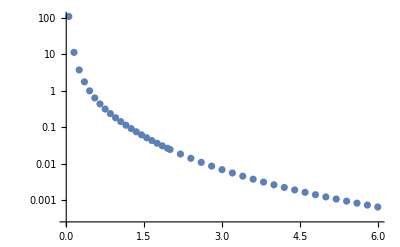

```mathematica
ListLogPlot[dσAvg]
```

```mathematica
ClearAll[dσV2];
dσV2=Join[{{0.05,{{-0.041652194784031905,0.040697198948238575,0.}}},{0.15000000000000002,{{-0.0448273912099484,0.00419614909015309,2.1872882687055003*^-16}}},{0.25,{{-0.03728072751969742,0.0013746481355415552,0.}}},{0.35000000000000003,{{-0.029323526394764866,0.0006392841403892771,6.31316439072433*^-17}}},{0.45,{{-0.022339278265243956,0.0003534502713324751,6.943772281604763*^-18}}},{0.55,{{-0.016624909293206844,0.00021852275433528596,0.}}},{0.6500000000000001,{{-0.012233145642991154,0.00014625664413039666,0.}}},{0.7500000000000001,{{-0.008857937201339051,0.0001033677227659424,2.4997580213777142*^-18}}},{0.8500000000000001,{{-0.006417679767117887,0.00007597041487919059,0.}}},{0.9500000000000001,{{-0.004656911023068994,0.000057839659502836544,0.}}},{1.05,{{-0.0034283978996111023,0.00004491793283927274,0.}}},{1.1500000000000001,{{-0.0025509281734393667,0.000035715875100133314,0.}}},{1.2500000000000002,{{-0.0019405066444709912,0.000028626878813173854,3.1496951069359193*^-18}}},{1.35,{{-0.0014894087202164319,0.00002327866630292029,4.243416394314022*^-18}}},{1.4500000000000002,{{-0.001180034129134045,0.000019181599920775476,1.0031728088168593*^-18}}},{1.55,{{-0.0009413942200587323,0.000016010982209717803,0.}}},{1.6500000000000001,{{-0.0007669523454671722,0.000013375542773816284,2.8406341152019483*^-18}}},{1.7500000000000002,{{-0.0006311741037669958,0.000011262241773140713,1.1478480710407872*^-18}}},{1.85,{{-0.0005210936101142312,9.571818394620674*^-6,0.}}},{1.9500000000000002,{{-0.00043303242607600794,8.255604502078341*^-6,0.}}}},{{2.,{{-0.0003991568070816744,7.688074414442885*^-6,3.515284717562412*^-19}}},{2.2,{{-0.0002846865658643962,5.740799771225214*^-6,0.}}},{2.4,{{-0.00020593128726653214,4.453615725114349*^-6,3.6617549141275124*^-19}}},{2.6,{{-0.00015093899316638633,3.4792604085615374*^-6,6.240150386205464*^-19}}},{2.8,{{-0.00011340154908419785,2.7992926132651664*^-6,9.882254486616783*^-17}}},{3.,{{-0.00008498428710252876,2.2582066769889198*^-6,7.01404759695228*^-14}}},{3.2,{{-0.00006352426061983032,1.8664379949043028*^-6,1.0581398349919305*^-13}}},{3.4000000000000004,{{-0.000048542159187592684,1.5397614840220162*^-6,2.190174424228128*^-14}}},{3.6,{{-0.00003826145177989256,1.2704227126077946*^-6,1.6452942931936789*^-15}}},{3.8,{{-0.00002998232665996279,1.0973127957271856*^-6,2.2385102202211254*^-11}}},{4.,{{-0.0000233411466655279,9.240870177845673*^-7,7.795706983441767*^-11}}},{4.2,{{-0.00001839154519678722,8.100799143794945*^-7,1.6888711141082588*^-13}}},{4.4,{{-0.000015105140775989588,6.936305882586469*^-7,2.2854728904513847*^-13}}},{4.6,{{-0.000012214798295624119,6.048152901676663*^-7,6.073927018995382*^-8}}},{4.800000000000001,{{-9.761263631156107*^-6,5.369003455063748*^-7,5.543274740696969*^-9}}},{5.,{{-7.845378030057287*^-6,4.7371684855497*^-7,2.6045838429024015*^-13}}},{5.2,{{-6.608662079715056*^-6,4.183303661551282*^-7,5.8331105766386035*^-15}}},{5.4,{{-5.426753597855835*^-6,3.739264427937166*^-7,4.453160857708942*^-10}}},{5.6,{{-4.963763919373535*^-6,3.3446708780845486*^-7,6.862753264270408*^-10}}},{5.800000000000001,{{-3.8010933374481607*^-6,2.9822175562636296*^-7,5.572122953077953*^-9}}},{6.,{{-3.097158926467118*^-6,2.7181752816947286*^-7,3.841516171489119*^-10}}}}
];
```

```mathematica
ClearAll[klist];
klist=dσAvg[[All,1]]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.0416522,-0.0448274,-0.0372807,-0.0293235,-0.0223393,-0.0166249,-0.0122331,-0.00885794,-0.00641768,-0.00465691,-0.0034284,-0.00255093,-0.00194051,-0.00148941,-0.00118003,-0.000941394,-0.000766952,-0.000631174,-0.000521094,-0.000433032,-0.000399157,-0.000284687,-0.000205931,-0.000150939,-0.000113402,-0.0000849843,-0.0000635243,-0.0000485422,-0.0000382615,-0.0000299823,-0.0000233411,-0.0000183915,-0.0000151051,-0.0000122148,-9.76126×10^-6,-7.84538×10^-6,-6.60866×10^-6,-5.42675×10^-6,-4.96376×10^-6,-3.80109×10^-6,-3.09716×10^-6}

{0.0406972,0.00419615,0.00137465,0.000639284,0.00035345,0.000218523,0.000146257,0.000103368,0.0000759704,0.0000578397,0.0000449179,0.0000357159,0.0000286269,0.0000232787,0.0000191816,0.000016011,0.0000133755,0.0000112622,9.57182×10^-6,8.2556×10^-6,7.68807×10^-6,5.7408×10^-6,4.45362×10^-6,3.47926×10^-6,2.79929×10^-6,2.25821×10^-6,1.86644×10^-6,1.53976×10^-6,1.27042×10^-6,1.09731×10^-6,9.24087×10^-7,8.1008×10^-7,6.93631×10^-7,6.04815×10^-7,5.369×10^-7,4.73717×10^-7,4.1833×10^-7,3.73926×10^-7,3.34467×10^-7,2.98222×10^-7,2.71818×10^-7}

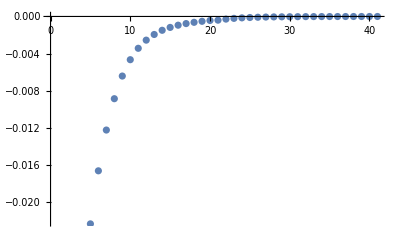

```mathematica
ListPlot[dσV2b]
```

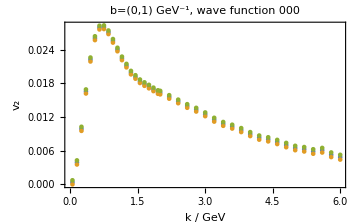

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{klist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"k / GeV","v_2"},ImageSize->Medium,PlotLabel->"b=(0,1) GeV^-1, wave function 000"]
```

## Scan b, 000 state, κ=0.61, mf=0.48

## k=1 GeV

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg=Join[{{0.1,0.2046391965590501},{0.2,0.20204004442503196},{0.30000000000000004,0.1982493828377517},{0.4,0.19387436037789438},{0.5,0.18891492901696375},{0.6,0.18365104897221776},{0.7000000000000001,0.17813863358470483},{0.8,0.1723951898849824},{0.9,0.16656178256604123},{1.,0.1606073906050193},{1.1,0.15490995332803556},{1.2000000000000002,0.1488573219973303},{1.3000000000000003,0.14292161060349934},{1.4000000000000001,0.1367504972803323},{1.5000000000000002,0.1307846927856534},{1.6,0.12482495271008587},{1.7000000000000002,0.11889523992199041},{1.8000000000000003,0.11306531178096905},{1.9000000000000001,0.1072957335218198},{2.,0.10166472378115794}},{{2.2,0.09092181959977694},{2.4000000000000004,0.08079617978357527},{2.6,0.07145994362531798},{2.8000000000000003,0.06304205509312345},{3.,0.05539550092265796},{3.2,0.04866945003606801},{3.4000000000000004,0.042693386793989346},{3.6000000000000005,0.03752744087231347},{3.8000000000000003,0.03296747112558552},{4.,0.029078804552084017},{4.2,0.025673970220407395},{4.4,0.022751934483339894},{4.6000000000000005,0.02020827150762139},{4.800000000000001,0.01804255331940869},{5.,0.016120716244268515},{5.2,0.014462769420006715},{5.4,0.013014092778055177},{5.6000000000000005,0.0117396360424992},{5.800000000000001,0.010616375471440004},{6.,0.009603002783621802}}
];
```

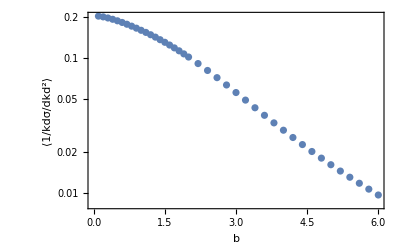

```mathematica
ListLogPlot[dσAvg,PlotRange->All,Frame->True,FrameLabel->{"b","⟨1/kdσ/dkd^2⟩"}]
```

```mathematica
ClearAll[dσV2];
dσV2=Join[{{0.1,{{-0.0002019591063853379,0.0000673611141409858,0.}}},{0.2,{{-0.0005676318636548417,0.00006521524308459922,7.030569435124824*^-19}}},{0.30000000000000004,{{-0.0011059234974103106,0.00006297449722975732,7.030569435124824*^-19}}},{0.4,{{-0.0016828448505234997,0.00006082241427402416,0.}}},{0.5,{{-0.002269725895021021,0.00005905124287781702,7.030569435124824*^-18}}},{0.6,{{-0.0027624123606322707,0.00005733575377500181,0.}}},{0.7000000000000001,{{-0.0031932359290566554,0.00005575646777863841,0.}}},{0.8,{{-0.0035451352697607316,0.000054093625707950844,0.}}},{0.9,{{-0.0038111312576791915,0.0000523380037369178,0.}}},{1.,{{-0.003985334814741131,0.000050972410745529365,7.030569435124824*^-18}}},{1.1,{{-0.004112897987676102,0.00004957036347248288,1.4061138870249648*^-18}}},{1.2000000000000002,{{-0.004119929596053476,0.00004816311879844998,0.}}},{1.3000000000000003,{{-0.004081370052856581,0.00004645948742245706,7.030569435124824*^-19}}},{1.4000000000000001,{{-0.0039969866622661014,0.00004470825557682042,0.}}},{1.5000000000000002,{{-0.003914896990823983,0.00004332387244842693,4.218341661074894*^-18}}},{1.6,{{-0.0037514565542211362,0.00004178140181553418,1.4061138870249648*^-18}}},{1.7000000000000002,{{-0.0036136513132760933,0.00004002441062829127,0.}}},{1.8000000000000003,{{-0.003457732159231596,0.00003816202452816749,7.733626378637306*^-18}}},{1.9000000000000001,{{-0.003319465742380704,0.000036578892618210806,0.}}},{2.,{{-0.0031777801626076438,0.00003487973667477385,7.030569435124824*^-18}}}},{{2.2,{{-0.002905766061526666,0.000031735300954286916,0.}}},{2.4000000000000004,{{-0.0026795911467490333,0.000028745296004486516,0.}}},{2.6,{{-0.002456498648819611,0.000025647473511953704,7.030569435124824*^-19}}},{2.8000000000000003,{{-0.002330519827431886,0.000023017094113703477,7.030569435124824*^-19}}},{3.,{{-0.002260769479143503,0.000020438103496328976,7.030569435124824*^-19}}},{3.2,{{-0.0022074098673323743,0.000018295646854620896,7.030569435124824*^-19}}},{3.4000000000000004,{{-0.0021737030825303505,0.000016377642562978933,2.8122277740499295*^-18}}},{3.6000000000000005,{{-0.0021754912780056865,0.000014751303969297314,0.}}},{3.8000000000000003,{{-0.0021551016318404922,0.00001301267451752047,0.}}},{4.,{{-0.0021398004195892634,0.000011533954048756473,2.8825334684011774*^-17}}},{4.2,{{-0.002112151302630861,0.000010319577617424234,1.476700804153618*^-14}}},{4.4,{{-0.0020853885077414965,9.178851282340014*^-6,1.2910937710663226*^-14}}},{4.6000000000000005,{{-0.0020361093346456132,8.224330924374625*^-6,2.8122277740499295*^-18}}},{4.800000000000001,{{-0.0019885219801497084,7.332766711255964*^-6,2.5310049966449366*^-17}}},{5.,{{-0.0019173591355973658,6.608034861239484*^-6,2.038865136186199*^-17}}},{5.2,{{-0.0018467646662712325,5.940543696917404*^-6,1.893951038989406*^-13}}},{5.4,{{-0.001767261753524771,5.350887502989277*^-6,1.0942251718578443*^-12}}},{5.6000000000000005,{{-0.0016800434012023064,4.798474448906769*^-6,2.910655746141677*^-16}}},{5.800000000000001,{{-0.0015900616653958131,4.36971960657595*^-6,1.414952578307415*^-11}}},{6.,{{-0.0014994455908461277,4.016243204687259*^-6,3.474507414838688*^-15}}}}
];
```

```mathematica
ClearAll[blist];
blist=dσAvg[[All,1]]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.000201959,-0.000567632,-0.00110592,-0.00168284,-0.00226973,-0.00276241,-0.00319324,-0.00354514,-0.00381113,-0.00398533,-0.0041129,-0.00411993,-0.00408137,-0.00399699,-0.0039149,-0.00375146,-0.00361365,-0.00345773,-0.00331947,-0.00317778,-0.00290577,-0.00267959,-0.0024565,-0.00233052,-0.00226077,-0.00220741,-0.0021737,-0.00217549,-0.0021551,-0.0021398,-0.00211215,-0.00208539,-0.00203611,-0.00198852,-0.00191736,-0.00184676,-0.00176726,-0.00168004,-0.00159006,-0.00149945}

{0.0000673611,0.0000652152,0.0000629745,0.0000608224,0.0000590512,0.0000573358,0.0000557565,0.0000540936,0.000052338,0.0000509724,0.0000495704,0.0000481631,0.0000464595,0.0000447083,0.0000433239,0.0000417814,0.0000400244,0.000038162,0.0000365789,0.0000348797,0.0000317353,0.0000287453,0.0000256475,0.0000230171,0.0000204381,0.0000182956,0.0000163776,0.0000147513,0.0000130127,0.000011534,0.0000103196,9.17885×10^-6,8.22433×10^-6,7.33277×10^-6,6.60803×10^-6,5.94054×10^-6,5.35089×10^-6,4.79847×10^-6,4.36972×10^-6,4.01624×10^-6}

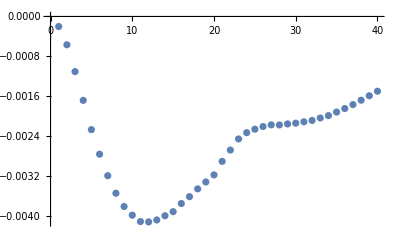

```mathematica
ListPlot[dσV2b]
```

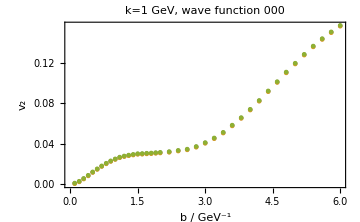

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{blist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"b / GeV^-1","v_2"},ImageSize->Medium,PlotLabel->"k=1 GeV, wave function 000"]
```

```mathematica
Export["blist000.dat",blist]
Export["dsV2bk1.dat",1/dσAvg[[All,2]] dσV2b]
Export["dsV2bk1err.dat",1/dσAvg[[All,2]] dσV2berr]
```

blist000.dat

dsV2bk1.dat

dsV2bk1err.dat

## k=0.1 GeV

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.1,39.14344990487078},{0.35,36.804429245919},{0.6,33.16849718410551},{0.85,29.19656543614694},{1.1,25.342195095781303},{1.35,21.830485949499355},{1.6,18.71975989372451},{2.1,13.66536855588475},{2.35,11.666791950697082},{2.6,9.943492049573077},{2.85,8.48414245130521},{3.1,7.236512737285706},{3.6,5.267521843827061},{3.85,4.498204955267034},{4.1,3.8432628689553865},{4.35,3.2918394629949654},{4.6,2.8234359545230103},{4.85,2.4246083154272884}};
```

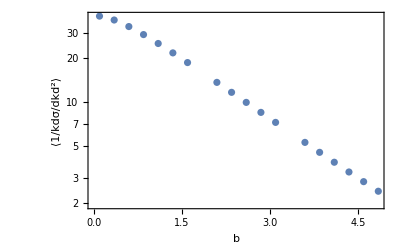

```mathematica
ListLogPlot[dσAvg,PlotRange->All,Frame->True,FrameLabel->{"b","⟨1/kdσ/dkd^2⟩"}]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.1,{{-0.008342515058887308,0.015733590220976975,7.030569435124823*^-17}}},{0.35,{{-0.0035205339398827044,0.014180047150321463,0.}}},{0.6,{{-0.026454653361702087,0.012389969731304129,0.}}},{0.85,{{-0.03542702638711679,0.010770423781667267,7.030569435124823*^-17}}},{1.1,{{-0.056489986229226206,0.009329517688942038,1.4061138870249645*^-16}}},{1.35,{{-0.06951258084744712,0.008095470524983902,2.1091708305374468*^-16}}},{1.6,{{-0.07315350113156278,0.006984543408617882,3.5152847175624113*^-16}}},{2.1,{{-0.08349251505809786,0.005260055751101076,2.1091708305374468*^-16}}},{2.35,{{-0.08993995581574571,0.004577025424765437,0.}}},{2.6,{{-0.08719716672682999,0.003949479176245453,0.}}},{2.85,{{-0.08115182613189004,0.003412289714969914,0.}}},{3.1,{{-0.07789858069898248,0.002960730886448666,0.}}},{3.6,{{-0.06709182838688507,0.0022198666202081943,2.812227774049929*^-16}}},{3.85,{{-0.0616253450873855,0.001924800171878615,0.}}},{4.1,{{-0.057654002803174814,0.0016695314103411748,2.0458957056213235*^-12}}},{4.35,{{-0.051899507412389335,0.0014592524761228385,8.436683322149787*^-16}}},{4.6,{{-0.046982046705338926,0.0012686914460006144,0.}}},{4.85,{{-0.042493538761948633,0.0010978171107087192,7.030569435124823*^-17}}}};
```

```mathematica
ClearAll[blist];
blist=dσAvg[[All,1]]
```

{0.1,0.35,0.6,0.85,1.1,1.35,1.6,2.1,2.35,2.6,2.85,3.1,3.6,3.85,4.1,4.35,4.6,4.85}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.00834252,-0.00352053,-0.0264547,-0.035427,-0.05649,-0.0695126,-0.0731535,-0.0834925,-0.08994,-0.0871972,-0.0811518,-0.0778986,-0.0670918,-0.0616253,-0.057654,-0.0518995,-0.046982,-0.0424935}

{0.0157336,0.01418,0.01239,0.0107704,0.00932952,0.00809547,0.00698454,0.00526006,0.00457703,0.00394948,0.00341229,0.00296073,0.00221987,0.0019248,0.00166953,0.00145925,0.00126869,0.00109782}

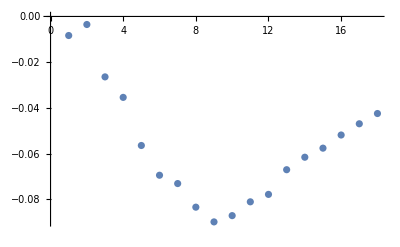

```mathematica
ListPlot[dσV2b]
```

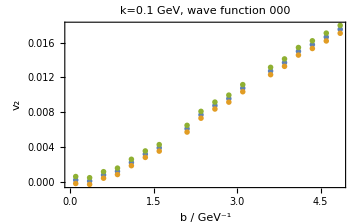

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{blist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"b / GeV^-1","v_2"},ImageSize->Medium,PlotLabel->"k=0.1 GeV, wave function 000"]
```

## k averaged from 0.2 GeV to 3 GeV

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg=Join[{{0.1,0.6107363056486849},{0.35,0.5794258236877833},{0.6,0.5327347562129257},{0.85,0.48153454891743075},{1.1,0.43103964444663423},{1.35,0.3830432057296123},{1.6,0.3379383422824065},{1.85,0.2968870124586733},{2.1,0.2591428299409911},{2.35,0.2255628820180927},{2.6,0.19533116215917334},{2.85,0.1686444273740353},{3.1,0.14504427795980437},{3.35,0.12448829091772327},{3.6,0.10672656746164635},{3.85,0.09132043258971011},{4.1,0.07820832765183007},{4.35,0.0668752154447598},{4.6,0.057308757301405985},{4.85,0.049171547317196015}},{{5.,0.04477864807992239},{5.25,0.038481996179687075},{5.5,0.0331538849992969},{5.75,0.028593978601027036},{6.,0.024703845452084153},{6.25,0.02142604553930789},{6.5,0.018610754582448194},{6.75,0.016209188194154622},{7.,0.014180626655859533},{7.25,0.012420792648186582},{7.5,0.010914832765473066},{7.75,0.009614048028534035},{8.,0.008510681254909206}}];
```

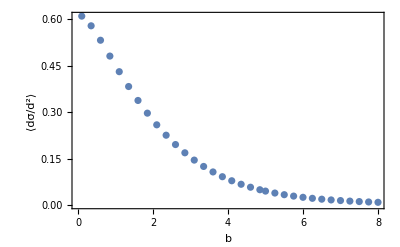

```mathematica
ListPlot[dσAvg,PlotRange->All,Frame->True,FrameLabel->{"b","⟨dσ/d^2⟩"}]
```

```mathematica
ClearAll[dσV2];
dσV2=Join[{{0.1,{{-0.00030499963281658665,0.0001296095319976686,7.733626378637306*^-18}}},{0.35,{{-0.0025117311825034786,0.00011807873774359324,0.}}},{0.6,{{-0.00526390338494466,0.00010655192551264615,2.8122277740499295*^-18}}},{0.85,{{-0.007544180893590349,0.00009575214816503725,5.624455548099859*^-18}}},{1.1,{{-0.009191273740939794,0.00008614478060284053,9.139740265662271*^-18}}},{1.35,{{-0.010047908632979831,0.00007740296077974866,0.}}},{1.6,{{-0.01038749195233978,0.00006912666843141246,4.921398604587377*^-18}}},{1.85,{{-0.010170846527521073,0.00006153412500786209,4.921398604587377*^-18}}},{2.1,{{-0.009753216147185982,0.000054566574092094785,0.}}},{2.35,{{-0.009078684465461598,0.000048259232614257093,0.}}},{2.6,{{-0.008259732112818292,0.00004201922921002016,0.}}},{2.85,{{-0.007447531724826729,0.00003679174241356874,0.}}},{3.1,{{-0.006657497380843,0.000031937658436287666,1.4061138870249648*^-18}}},{3.35,{{-0.005903189799030308,0.00002788686498620246,0.}}},{3.6,{{-0.005206147543115137,0.00002429658402249829,0.}}},{3.85,{{-0.0045993528407639135,0.000021109627057103674,1.4061138870249648*^-18}}},{4.1,{{-0.004057482025216244,0.000018375106949359087,0.}}},{4.35,{{-0.0035671026711271577,0.0000158976884491243,0.}}},{4.6,{{-0.0031418050252186615,0.000013855175466059614,7.030569435124824*^-19}}},{4.85,{{-0.002765887793172943,0.000012034997379761343,6.327512491612341*^-18}}}},{{5.,{{-0.0025687454609308164,0.000011041130339548927,2.8122277740499295*^-18}}},{5.25,{{-0.0022691305723424914,9.64278402680519*^-6,0.}}},{5.5,{{-0.00201606243122,8.376117943514112*^-6,9.139740265662271*^-18}}},{5.75,{{-0.0017921608885211565,7.415954873386333*^-6,0.}}},{6.,{{-0.0015980349988300958,6.459633870831707*^-6,5.624455548099859*^-18}}},{6.25,{{-0.001431591227100522,5.618247000610658*^-6,0.}}},{6.5,{{-0.0012807402729834885,4.9374963624993216*^-6,6.327512491612341*^-18}}},{6.75,{{-0.0011569822675188272,4.298071140095452*^-6,5.624455548099859*^-18}}},{7.,{{-0.0010379495614123524,3.804400726906447*^-6,0.}}},{7.25,{{-0.000943753605672977,3.368715551404661*^-6,9.139740265662271*^-18}}},{7.5,{{-0.0008537476117814096,2.9841179918624126*^-6,0.}}},{7.75,{{-0.0007794256811583568,2.679123633245277*^-6,0.}}},{8.,{{-0.0007080616792941834,2.342525945225103*^-6,0.}}}}];
```

```mathematica
ClearAll[blist];
blist=dσAvg[[All,1]]
```

{0.1,0.35,0.6,0.85,1.1,1.35,1.6,1.85,2.1,2.35,2.6,2.85,3.1,3.35,3.6,3.85,4.1,4.35,4.6,4.85,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.000305,-0.00251173,-0.0052639,-0.00754418,-0.00919127,-0.0100479,-0.0103875,-0.0101708,-0.00975322,-0.00907868,-0.00825973,-0.00744753,-0.0066575,-0.00590319,-0.00520615,-0.00459935,-0.00405748,-0.0035671,-0.00314181,-0.00276589,-0.00256875,-0.00226913,-0.00201606,-0.00179216,-0.00159803,-0.00143159,-0.00128074,-0.00115698,-0.00103795,-0.000943754,-0.000853748,-0.000779426,-0.000708062}

{0.00012961,0.000118079,0.000106552,0.0000957521,0.0000861448,0.000077403,0.0000691267,0.0000615341,0.0000545666,0.0000482592,0.0000420192,0.0000367917,0.0000319377,0.0000278869,0.0000242966,0.0000211096,0.0000183751,0.0000158977,0.0000138552,0.000012035,0.0000110411,9.64278×10^-6,8.37612×10^-6,7.41595×10^-6,6.45963×10^-6,5.61825×10^-6,4.9375×10^-6,4.29807×10^-6,3.8044×10^-6,3.36872×10^-6,2.98412×10^-6,2.67912×10^-6,2.34253×10^-6}

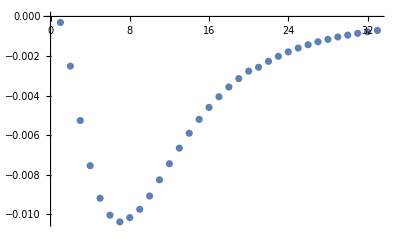

```mathematica
ListPlot[dσV2b]
```

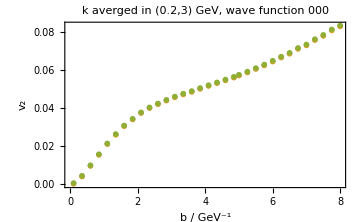

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{blist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"b / GeV^-1","v_2"},ImageSize->Medium,PlotLabel->"k averged in (0.2,3) GeV, wave function 000"]
```

## Scan k, 000 state, κ=1.34, mf=1.27

## b=(0,1) GeV^-1

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.05,52.43244888391814},{0.3,1.3709204047495434},{0.55,0.38749555943870717},{0.8,0.17811515388525984},{1.05,0.10144674586322684},{1.3,0.06464772651343534},{1.55,0.04388055667497128},{1.8,0.03103078470966283},{2.05,0.022609664111462844},{2.3,0.016899382364283597},{2.55,0.012886860608539106},{2.8,0.010008702051308343},{3.05,0.007910317316892573},{3.3,0.006339768024298459},{3.55,0.0051471369727914785},{3.8,0.0042174685979915714},{4.05,0.003489631111023194},{4.3,0.002912870216063861},{4.55,0.002446489675578404},{4.8,0.0020710135647181984}};
```

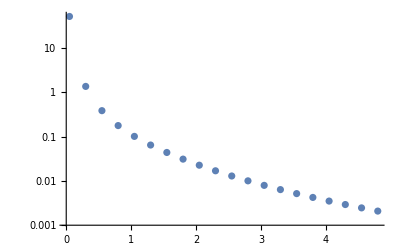

```mathematica
ListLogPlot[dσAvg]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.05,{{-0.022026248303773782,0.0198057321731321,5.624455548099858*^-16}}},{0.3,{{-0.017865973331185878,0.0005215641661805643,7.81174381680536*^-18}}},{0.55,{{-0.012708117598094355,0.00014644929158850534,0.}}},{0.8,{{-0.008340214128554931,0.00006585979560725386,0.}}},{1.05,{{-0.005172246781132238,0.00003673188581506744,1.275386745600875*^-18}}},{1.3,{{-0.003119602987438365,0.0000228142969384316,1.2480300772410927*^-18}}},{1.55,{{-0.0018679318399693107,0.000015252558744033287,2.926355644172663*^-19}}},{1.8,{{-0.0011544411055901752,0.000010729309974717344,1.5189501866010423*^-18}}},{2.05,{{-0.0007617724952814009,7.758707273104064*^-6,1.0037695802676728*^-18}}},{2.3,{{-0.0005574696895916168,5.765319899595108*^-6,1.0632241111719964*^-18}}},{2.55,{{-0.00044303617729964,4.373650306748352*^-6,2.1624204337177466*^-19}}},{2.8,{{-0.000372009319722149,3.3932054470841967*^-6,3.5870252220024613*^-19}}},{3.05,{{-0.00032328920136688713,2.664246110373707*^-6,3.778860217750511*^-19}}},{3.3,{{-0.0002784225746576657,2.1267566249053744*^-6,0.}}},{3.55,{{-0.0002409043725572152,1.7289364502349392*^-6,0.}}},{3.8,{{-0.0002046525753797177,1.410381404715181*^-6,1.4606446194857667*^-19}}},{4.05,{{-0.00017301949262750013,1.1681337764913865*^-6,5.143535023410937*^-19}}},{4.3,{{-0.0001455472091732963,9.750868533788645*^-7,2.4715360372261416*^-18}}},{4.55,{{-0.00012096851670144279,8.396892733404804*^-7,1.6980001050899227*^-17}}},{4.8,{{-0.00010131481774709909,7.045473916345002*^-7,8.293874880498815*^-17}}}};
```

```mathematica
ClearAll[klist];
klist=dσAvg[[All,1]]
```

{0.05,0.3,0.55,0.8,1.05,1.3,1.55,1.8,2.05,2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.0220262,-0.017866,-0.0127081,-0.00834021,-0.00517225,-0.0031196,-0.00186793,-0.00115444,-0.000761772,-0.00055747,-0.000443036,-0.000372009,-0.000323289,-0.000278423,-0.000240904,-0.000204653,-0.000173019,-0.000145547,-0.000120969,-0.000101315}

{0.0198057,0.000521564,0.000146449,0.0000658598,0.0000367319,0.0000228143,0.0000152526,0.0000107293,7.75871×10^-6,5.76532×10^-6,4.37365×10^-6,3.39321×10^-6,2.66425×10^-6,2.12676×10^-6,1.72894×10^-6,1.41038×10^-6,1.16813×10^-6,9.75087×10^-7,8.39689×10^-7,7.04547×10^-7}

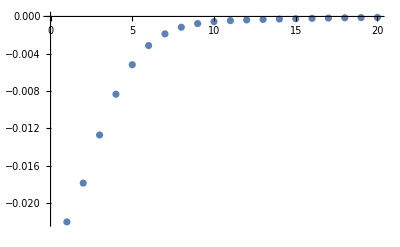

```mathematica
ListPlot[dσV2b]
```

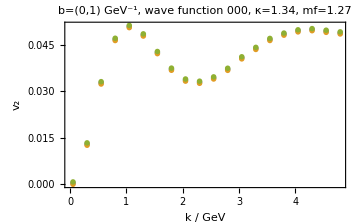

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{klist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"k / GeV","v_2"},ImageSize->Medium,PlotLabel->"b=(0,1) GeV^-1, wave function 000, κ=1.34, mf=1.27"]
```

```mathematica
Export["klistJ.dat",klist]
Export["dsV2berrJ.dat",1/dσAvg[[All,2]] dσV2berr]
Export["dsV2bJ.dat",1/dσAvg[[All,2]] dσV2b]
```

klistJ.dat

dsV2berrJ.dat

dsV2bJ.dat

## Scan k, nlm-summed state

## b=(0,1) GeV^-1

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.05,88.81494350689621},{0.3,2.202847751619753},{0.55,0.5936115088259216},{0.8,0.25928261042743916},{1.05,0.13885383988708688},{1.3,0.08286065814818905},{1.55,0.052920156417239114},{1.8,0.035499028071662456},{2.05,0.0247479282365243},{2.3,0.017805211093329783},{2.55,0.013136577091579222},{2.8,0.00989793700354008},{3.05,0.00759765968121135},{3.3,0.005931665639843353},{3.55,0.004695797765934292},{3.8,0.0037632297957161352},{4.05,0.0030583348671957803},{4.3,0.002502616957955865},{4.55,0.002072312485852963},{4.8,0.0017317646237691418}};
```

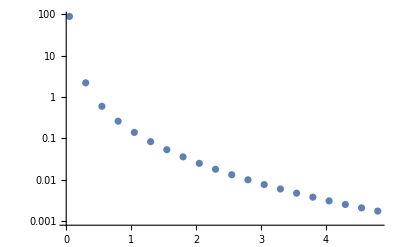

```mathematica
ListLogPlot[dσAvg]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.05,{{-0.01318174694865025,0.02559151023173142,1.5901571324106926*^-15}}},{0.3,{{-0.018068690981737252,0.0006240058636876585,0.}}},{0.55,{{-0.010446623255830395,0.00016081775879887825,1.020797548622057*^-17}}},{0.8,{{-0.005668700755408251,0.00006704056766557879,5.190302477170742*^-18}}},{1.05,{{-0.003106310152000867,0.00003484515193907106,2.4176517830144767*^-18}}},{1.3,{{-0.0018484057197561965,0.000020388099459990782,1.4189459775349997*^-18}}},{1.55,{{-0.0012455097893662183,0.000012918232891826095,0.}}},{1.8,{{-0.0009295710846644398,8.594661087071862*^-6,3.406447703164149*^-18}}},{2.05,{{-0.0007312342533652143,5.990571956319936*^-6,0.}}},{2.3,{{-0.0005785822000318919,4.2958264606479695*^-6,0.}}},{2.55,{{-0.00045438567427669873,3.174463445656644*^-6,1.9859563090019663*^-19}}},{2.8,{{-0.00035568806645596253,2.4111067960352855*^-6,5.576447955122539*^-19}}},{3.05,{{-0.0002754069592840433,1.8602373389267507*^-6,3.8340057006852434*^-19}}},{3.3,{{-0.0002133488554964758,1.462190713948481*^-6,2.674685062245495*^-19}}},{3.55,{{-0.00016480875798507676,1.1713328689903633*^-6,9.29397075984821*^-19}}},{3.8,{{-0.00012862509569801215,9.486690131405714*^-7,0.}}},{4.05,{{-0.00010093924774343307,7.81991059617069*^-7,0.}}},{4.3,{{-0.00007933316055719591,6.490161470575166*^-7,0.}}},{4.55,{{-0.00006240866211490551,5.44833078275273*^-7,1.672874512739085*^-17}}},{4.8,{{-0.00005019718046418451,4.626713042082713*^-7,1.0103419461655211*^-19}}}};
```

```mathematica
ClearAll[klist];
klist=dσAvg[[All,1]]
```

{0.05,0.3,0.55,0.8,1.05,1.3,1.55,1.8,2.05,2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.0131817,-0.0180687,-0.0104466,-0.0056687,-0.00310631,-0.00184841,-0.00124551,-0.000929571,-0.000731234,-0.000578582,-0.000454386,-0.000355688,-0.000275407,-0.000213349,-0.000164809,-0.000128625,-0.000100939,-0.0000793332,-0.0000624087,-0.0000501972}

{0.0255915,0.000624006,0.000160818,0.0000670406,0.0000348452,0.0000203881,0.0000129182,8.59466×10^-6,5.99057×10^-6,4.29583×10^-6,3.17446×10^-6,2.41111×10^-6,1.86024×10^-6,1.46219×10^-6,1.17133×10^-6,9.48669×10^-7,7.81991×10^-7,6.49016×10^-7,5.44833×10^-7,4.62671×10^-7}

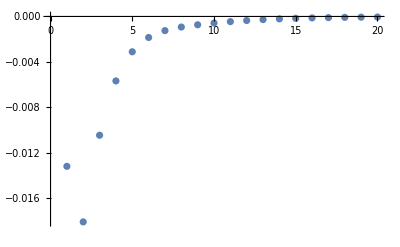

```mathematica
ListPlot[dσV2b]
```

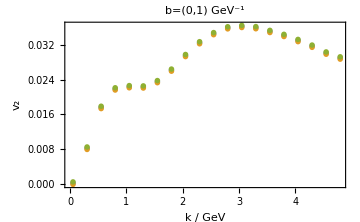

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{klist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"k / GeV","v_2"},ImageSize->Medium,PlotLabel->"b=(0,1) GeV^-1"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bwu/Documents/v2

```mathematica
Export["klistresum.dat",klist]
Export["dsV2berrresum.dat",1/dσAvg[[All,2]] dσV2berr]
Export["dsV2bresum.dat",1/dσAvg[[All,2]] dσV2b]
```

klistresum.dat

dsV2berrresum.dat

dsV2bresum.dat

## b=(0, 0.5) GeV^-1

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.3,3.0763547824220034},{0.55,0.8074834767166509},{0.8,0.34585094975175956},{1.05,0.1843268662945871},{1.3,0.11036941991117118},{1.55,0.07095321419480866},{1.8,0.0478727301642176},{2.05,0.03354074105153487},{2.3,0.024226965408321803},{2.55,0.01793370169362843},{2.8,0.013564019298623201},{3.05,0.010469166457152648},{3.3,0.008203714634312645},{3.55,0.006524953242058279},{3.8,0.005258809008046635},{4.05,0.0042872066072989065},{4.3,0.0035283936587210316},{4.55,0.002935200096741124},{4.8,0.0024601758300823577}};
```

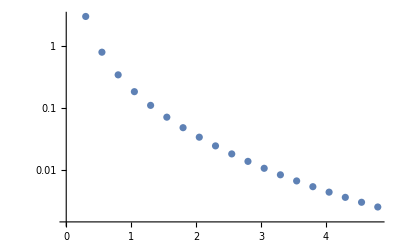

```mathematica
ListLogPlot[dσAvg]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.3,{{-0.008296601164368235,0.0009074270699456354,2.3030751304069172*^-17}}},{0.55,{{-0.005930203777412302,0.00022636351786854429,5.3854093522320496*^-18}}},{0.8,{{-0.0036426854884783096,0.00009135347463383899,6.768077067476208*^-18}}},{1.05,{{-0.00220892630666186,0.00004629363941713319,6.740192902957987*^-19}}},{1.3,{{-0.001371821216149676,0.00002686028961902166,1.1853790664456563*^-18}}},{1.55,{{-0.0008902860814105618,0.00001689631536968317,0.}}},{1.8,{{-0.0006112564245723141,0.000011289141908989747,7.266313097941436*^-19}}},{2.05,{{-0.00044210111781209653,7.915935690025554*^-6,0.}}},{2.3,{{-0.00032676582418416305,5.697355508740814*^-6,0.}}},{2.55,{{-0.0002485162528977217,4.268413807328476*^-6,0.}}},{2.8,{{-0.00019267164040091513,3.2283178308210644*^-6,0.}}},{3.05,{{-0.00014889657319124274,2.5305838813128027*^-6,2.3608141575334624*^-19}}},{3.3,{{-0.00011557278885383785,1.9940761633394384*^-6,1.5266688684902228*^-19}}},{3.55,{{-0.00009180033864146702,1.5992771536068744*^-6,1.2885959645731993*^-20}}},{3.8,{{-0.00007280382735199205,1.2980995857455982*^-6,0.}}},{4.05,{{-0.00005742938242618902,1.0757029892943019*^-6,0.}}},{4.3,{{-0.000046604619817220826,8.970456459960786*^-7,3.926753082956552*^-19}}},{4.55,{{-0.00003704485740814163,7.545711837587862*^-7,1.7729377521033445*^-15}}},{4.8,{{-0.000030158829310763428,6.388222590872699*^-7,0.}}}};
```

```mathematica
ClearAll[klist];
klist=dσAvg[[All,1]]
```

{0.3,0.55,0.8,1.05,1.3,1.55,1.8,2.05,2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.0082966,-0.0059302,-0.00364269,-0.00220893,-0.00137182,-0.000890286,-0.000611256,-0.000442101,-0.000326766,-0.000248516,-0.000192672,-0.000148897,-0.000115573,-0.0000918003,-0.0000728038,-0.0000574294,-0.0000466046,-0.0000370449,-0.0000301588}

{0.000907427,0.000226364,0.0000913535,0.0000462936,0.0000268603,0.0000168963,0.0000112891,7.91594×10^-6,5.69736×10^-6,4.26841×10^-6,3.22832×10^-6,2.53058×10^-6,1.99408×10^-6,1.59928×10^-6,1.2981×10^-6,1.0757×10^-6,8.97046×10^-7,7.54571×10^-7,6.38822×10^-7}

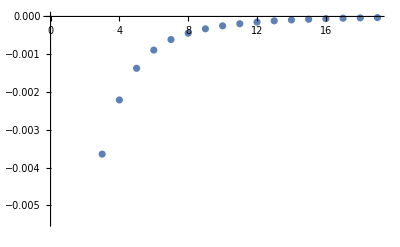

```mathematica
ListPlot[dσV2b]
```

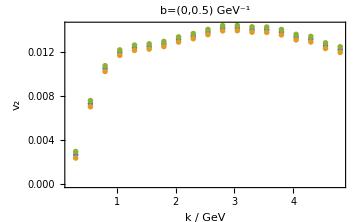

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{klist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{klist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"k / GeV","v_2"},ImageSize->Medium,PlotLabel->"b=(0,0.5) GeV^-1"]
```

## Scan b, nlm-summed state

## k=1 GeV

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.05,0.2378124696402835},{0.35,0.2204343478641915},{0.65,0.19165541679475104},{0.95,0.16074593567680726},{1.25,0.13154294431302233},{1.55,0.10591269628723894},{1.8499999999999999,0.08443291944287369},{2.15,0.06690644886515873},{2.4499999999999997,0.05286427632005384},{2.7499999999999996,0.04179610714876321},{3.05,0.03320125560335901},{3.3499999999999996,0.026449811057077798},{3.6499999999999995,0.021268113951599367},{3.9499999999999997,0.01723323134664208},{4.25,0.014094797752686834},{4.55,0.011654966643966569},{4.85,0.009702588456993008},{5.1499999999999995,0.00814222758045647},{5.449999999999999,0.006894429819022311},{5.75,0.005865086920246513}};
```

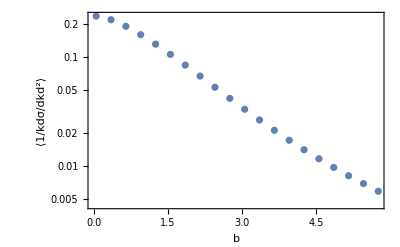

```mathematica
ListLogPlot[dσAvg,PlotRange->All,Frame->True,FrameLabel->{"b","⟨1/kdσ/dkd^2⟩"}]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.05,{{0.000013564476654081852,0.00006404357188717069,5.266502673929599*^-19}}},{0.35,{{-0.0016211221090035248,0.00005656029170694973,3.3002406260727745*^-19}}},{0.65,{{-0.0030813109141656484,0.000048489606158109644,5.083704453939177*^-18}}},{0.95,{{-0.0034990968795153682,0.00004049010328037348,2.0629583289675135*^-18}}},{1.25,{{-0.003195755001893286,0.00003352823927884886,0.}}},{1.55,{{-0.0027455826747758974,0.00002751487864545776,0.}}},{1.8499999999999999,{{-0.0022417168725839738,0.0000227511516755153,0.}}},{2.15,{{-0.0017979675121667293,0.000018885529037159576,0.}}},{2.4499999999999997,{{-0.0015116174512579271,0.000015792957665004627,0.}}},{2.7499999999999996,{{-0.0013266055578722606,0.000013169567768292265,3.0014117153158087*^-18}}},{3.05,{{-0.001222837896647682,0.000011031584200909702,0.}}},{3.3499999999999996,{{-0.0011796405969417203,9.330425808300178*^-6,0.}}},{3.6499999999999995,{{-0.0011375543238161094,7.938976598582203*^-6,5.132006963820775*^-18}}},{3.9499999999999997,{{-0.0011145696202292312,6.634524143373011*^-6,3.489789193766056*^-18}}},{4.25,{{-0.0010676310199541651,5.572474332690222*^-6,6.4403029660642*^-13}}},{4.55,{{-0.0010209210538493396,4.750704792023942*^-6,2.168034838991077*^-12}}},{4.85,{{-0.0009631397681949626,3.954557412495511*^-6,3.973172463472316*^-11}}},{5.1499999999999995,{{-0.0008930756783471118,3.4557016540066633*^-6,1.4176627788404276*^-9}}},{5.449999999999999,{{-0.0008214466458576921,2.921217142736895*^-6,6.723752567197521*^-6}}},{5.75,{{-0.0007493800564963104,2.5058811244966397*^-6,0.00003183483919526201}}}};
```

```mathematica
ClearAll[blist];
blist=dσAvg[[All,1]]
```

{0.05,0.35,0.65,0.95,1.25,1.55,1.85,2.15,2.45,2.75,3.05,3.35,3.65,3.95,4.25,4.55,4.85,5.15,5.45,5.75}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{0.0000135645,-0.00162112,-0.00308131,-0.0034991,-0.00319576,-0.00274558,-0.00224172,-0.00179797,-0.00151162,-0.00132661,-0.00122284,-0.00117964,-0.00113755,-0.00111457,-0.00106763,-0.00102092,-0.00096314,-0.000893076,-0.000821447,-0.00074938}

{0.0000640436,0.0000565603,0.0000484896,0.0000404901,0.0000335282,0.0000275149,0.0000227512,0.0000188855,0.000015793,0.0000131696,0.0000110316,9.33043×10^-6,7.93898×10^-6,6.63452×10^-6,5.57247×10^-6,4.7507×10^-6,3.95456×10^-6,3.4557×10^-6,2.92122×10^-6,2.50588×10^-6}

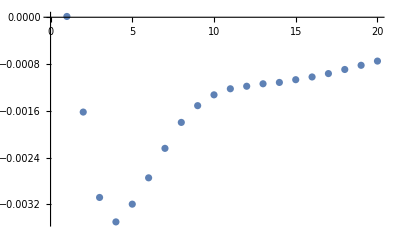

```mathematica
ListPlot[dσV2b]
```

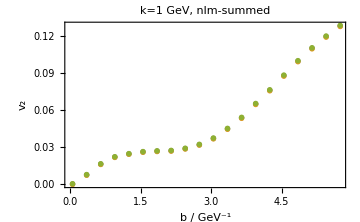

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{blist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"b / GeV^-1","v_2"},ImageSize->Medium,PlotLabel->"k=1 GeV, nlm-summed"]
```

## k averaged from 0.2 GeV to 3 GeV

Averge dσ

```mathematica
ClearAll[dσAvg]
dσAvg={{0.1,0.6761317377824521},{0.35,0.625013288500025},{0.6,0.5504011268160203},{0.85,0.47136887858246446},{1.1,0.39701179260374403},{1.35,0.3306808608796455},{1.6,0.27352255072703263},{1.85,0.22581463334367355},{2.1,0.18591322584408657},{2.35,0.153070954770926},{2.6,0.12617661208353323},{2.85,0.10418950441849817},{3.1,0.08622733419481902},{3.35,0.07156969383728581},{3.6,0.05948037594562327},{3.85,0.049673081404925684},{4.1,0.041624006388691896},{4.35,0.03498005077864629},{4.6,0.029480926796397848},{4.85,0.02494469664819675}};
```

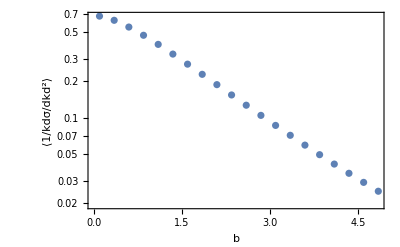

```mathematica
ListLogPlot[dσAvg,PlotRange->All,Frame->True,FrameLabel->{"b","⟨1/kdσ/dkd^2⟩"}]
```

```mathematica
ClearAll[dσV2];
dσV2={{0.1,{{-0.00046680171825257117,0.00016181537867093044,5.624455548099859*^-18}}},{0.35,{{-0.0030083962435966042,0.0001426186660257146,0.}}},{0.6,{{-0.0054730439541351445,0.00012288609878238947,4.921398604587377*^-18}}},{0.85,{{-0.006960925751150677,0.0001040674479819565,3.515284717562412*^-18}}},{1.1,{{-0.007569516873791339,0.00008743562663142601,1.4061138870249648*^-18}}},{1.35,{{-0.007621905968174831,0.00007314616875587667,7.030569435124824*^-19}}},{1.6,{{-0.0072388012138168,0.00006172188532427346,2.109170830537447*^-18}}},{1.85,{{-0.006787965247994159,0.00005201660200124306,7.030569435124824*^-19}}},{2.1,{{-0.006148615208899335,0.00004413192684399016,9.139740265662271*^-18}}},{2.35,{{-0.0054850228836383465,0.000037663758339185265,0.}}},{2.6,{{-0.004878176157908459,0.00003232425486043123,2.109170830537447*^-18}}},{2.85,{{-0.004276626131445235,0.00002755794745267955,2.8122277740499295*^-18}}},{3.1,{{-0.003724633391467326,0.000023741293207526487,0.}}},{3.35,{{-0.0032468412476745114,0.00002061682697326978,7.733626378637306*^-18}}},{3.6,{{-0.002835826921789726,0.00001794208669281266,4.921398604587377*^-18}}},{3.85,{{-0.0024614068368530415,0.000015567958403378698,1.3512754454309912*^-15}}},{4.1,{{-0.002149941859589199,0.000013609912299845282,3.501223578692162*^-16}}},{4.35,{{-0.0018681694030783262,0.000011855103375331106,2.8332627456599625*^-11}}},{4.6,{{-0.001632869050635387,0.00001033100412824565,3.170611894673749*^-11}}},{4.85,{{-0.0014265372264333062,9.054291027020762*^-6,1.3580522113095079*^-12}}}};
```

```mathematica
ClearAll[blist];
blist=dσAvg[[All,1]]
```

{0.1,0.35,0.6,0.85,1.1,1.35,1.6,1.85,2.1,2.35,2.6,2.85,3.1,3.35,3.6,3.85,4.1,4.35,4.6,4.85}

```mathematica
dσAvg[[All,1]]==dσV2[[All,1]]
```

True

```mathematica
ClearAll[dσV2b,dσV2berr];
dσV2b=Table[dσV2[[ii,2,1,1]],{ii,1,Length[dσV2]}]
dσV2berr=Table[dσV2[[ii,2,1,2]],{ii,1,Length[dσV2]}]
```

{-0.000466802,-0.0030084,-0.00547304,-0.00696093,-0.00756952,-0.00762191,-0.0072388,-0.00678797,-0.00614862,-0.00548502,-0.00487818,-0.00427663,-0.00372463,-0.00324684,-0.00283583,-0.00246141,-0.00214994,-0.00186817,-0.00163287,-0.00142654}

{0.000161815,0.000142619,0.000122886,0.000104067,0.0000874356,0.0000731462,0.0000617219,0.0000520166,0.0000441319,0.0000376638,0.0000323243,0.0000275579,0.0000237413,0.0000206168,0.0000179421,0.000015568,0.0000136099,0.0000118551,0.000010331,9.05429×10^-6}

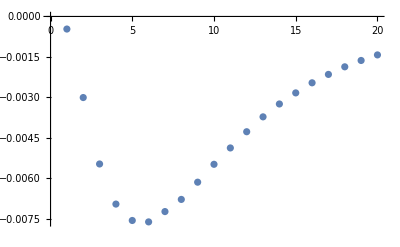

```mathematica
ListPlot[dσV2b]
```

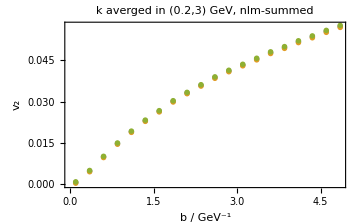

```mathematica
ClearAll[pic];
pic=ListPlot[{Transpose[{blist,-1/dσAvg[[All,2]]dσV2b}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b+dσV2berr)}],Transpose[{blist,-1/dσAvg[[All,2]](dσV2b-dσV2berr)}]},PlotRange->All,Frame->True,FrameLabel->{"b / GeV^-1","v_2"},ImageSize->Medium,PlotLabel->"k averged in (0.2,3) GeV, nlm-summed"]
```